# Radial Offset

## streakline.c

version 8 -  initial positions of ejected stars 
NFW parameters = {417.0 * pow(10,3) * mau * secyr, 36.54 * kpcau, 90.0 * pi / 180, 1.0, 1.0, 0.94}
offset = 0.2, 0.2
N = 6000, dt = 1,000,000 years, M = 1
Mass of Cluster = 20,000 Msun (no mass loss)
Initial Position of Cluster = 50 kpc,0,0
Initial Velocity of Cluster = 0.5 * centripetal velocity
Rcl = 20 pc = 4.126 * 10^6 AU

```mathematica
c8cl = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest8.csv",{"Data",6001,1;;2}];
c8dt =Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest8.csv",{"Data",2;;6000,1;;2}];
c8lt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest8.csv",{"Data",2;;6000,3;;4}];
c8ltv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest8.csv",{"Data",2;;6000,5;;6}];
c8tt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest8.csv",{"Data",2;;6000,7;;8}];
c8ttv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest8.csv",{"Data",2;;6000,9;;10}];
```

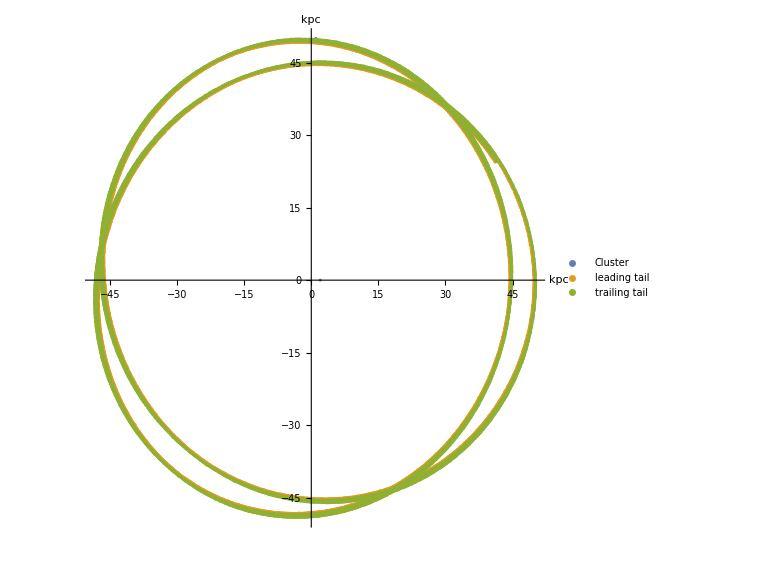

```mathematica
c8graph = ListPlot[{c8cl,c8lt,c8tt},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"Cluster","leading tail","trailing tail"},AxesLabel->{"kpc","kpc"}]
```

version 9 -  snapshot at 6000th timestep
NFW parameters = {417.0 * pow(10,3) * mau * secyr, 36.54 * kpcau, 90.0 * pi / 180, 1.0, 1.0, 0.94}
offset = 1.0,1.0
N = 6000, dt = 1,000,000 years, M = 1
Mass of Cluster = 20,000 Msun (no mass loss)
Initial Position of Cluster = 50 kpc,0,0
Initial Velocity of Cluster = 0.5 * centripetal velocity
Rcl = 20 pc = 4.126 * 10^6 AU

```mathematica
c9cl = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest9.csv",{"Data",3;;6000,1;;2}];
c9dt =Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest9.csv",{"Data",2,1;;12000}]
c9lt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest9.csv",{"Data",3;;6000,3;;4}];
c9ltv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest9.csv",{"Data",3;;6000,5;;6}];
c9tt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest9.csv",{"Data",3;;6000,7;;8}];
c9ttv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest9.csv",{"Data",3;;6000,9;;10}];
```

{0.2915509482051372725,0.5838086570718550306,0.3641036688777631869,0.790957873036215009,0.53196540443462903,0.4577047185247929417,0.1419054246422924437,11986,0.6712116104305759778,0.9667512481217866993,0.6957857757610157456,1.0137497862328066489,0.6707318259299404062,41.3840856140300203947,24.3423314042767273691}
 |  |  |  |

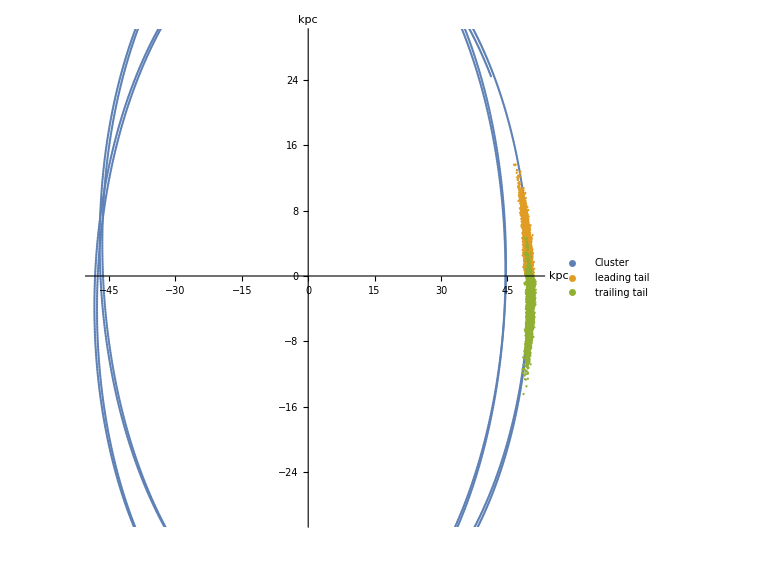

```mathematica
c9graph = ListPlot[{c9cl,c9lt,c9tt},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"Cluster","leading tail","trailing tail"},AxesLabel->{"kpc","kpc"}]
```

## streakline.chpl

version 21 - initial positions of stars at ejection (using c’s radial offsets)
NFW parameters = {417.0 * pow(10,3) * mau * secyr, 36.54 * kpcau, 90.0 * pi / 180, 1.0, 1.0, 0.94}
offset = 0.2, 0.2
N = 6000, dt = 1,000,000 years, M = 1
Mass of Cluster = 20,000 Msun (no mass loss)
Initial Position of Cluster = 50 kpc,0,0
Initial Velocity of Cluster = 0.5 * centripetal velocity
Rcl = 20 pc = 4.126 * 10^6 AU

```mathematica
ch21cl = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test21.csv",{"Data",6001,1;;2}];
ch21dt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test21.csv",{"Data",2;;6000,1;;2}];
ch21lt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test21.csv",{"Data",2;;6000,3;;4}];
ch21ltv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test21.csv",{"Data",2;;6000,5;;6}];
ch21tt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test21.csv",{"Data",2;;6000,7;;8}];
ch21ttv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test21.csv",{"Data",2;;6000,9;;10}];
```

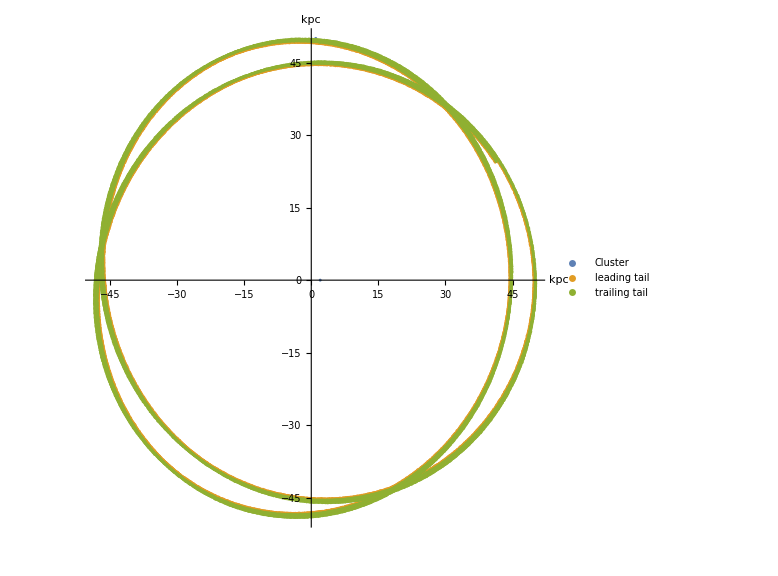

```mathematica
ch21graph = ListPlot[{ch21cl,ch21lt,ch21tt},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"Cluster","leading tail","trailing tail"},AxesLabel->{"kpc","kpc"}]
```

version 22 - initial positions of stars at ejection (using chapel’s random numbers)
NFW parameters = {417.0 * pow(10,3) * mau * secyr, 36.54 * kpcau, 90.0 * pi / 180, 1.0, 1.0, 0.94}
offset = 0.2, 0.2
N = 6000, dt = 1,000,000 years, M = 1
Mass of Cluster = 20,000 Msun (no mass loss)
Initial Position of Cluster = 50 kpc,0,0
Initial Velocity of Cluster = 0.5 * centripetal velocity
Rcl = 20 pc = 4.126 * 10^6 AU

```mathematica
ch22cl = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test22.csv",{"Data",6001,1;;2}];
ch22dt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test22.csv",{"Data",2;;6000,1;;2}];
ch22lt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test22.csv",{"Data",2;;6000,3;;4}];
ch22ltv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test22.csv",{"Data",2;;6000,5;;6}];
ch22tt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test22.csv",{"Data",2;;6000,7;;8}];
ch22ttv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test22.csv",{"Data",2;;6000,9;;10}];
```

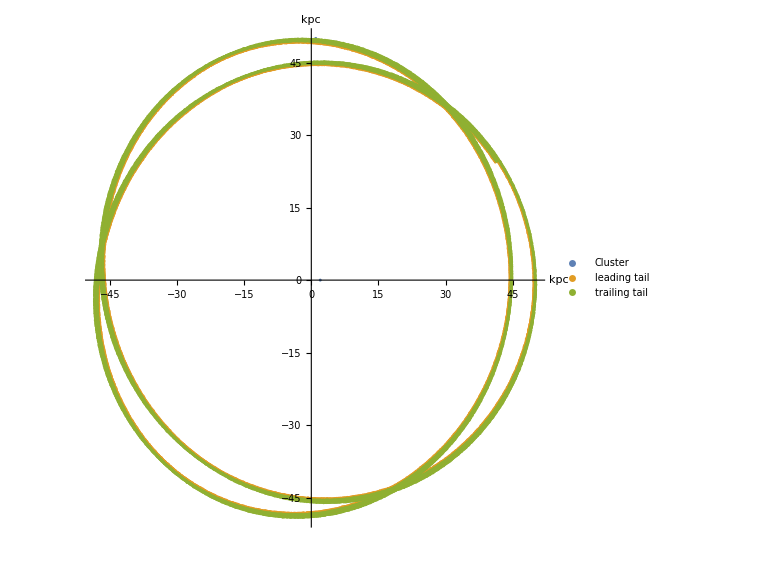

```mathematica
ch22graph = ListPlot[{ch22cl,ch22lt,ch22tt},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"Cluster","leading tail","trailing tail"},AxesLabel->{"kpc","kpc"}]
```

version 23 -snapshot at 6000th timestep
NFW parameters = {417.0 * pow(10,3) * mau * secyr, 36.54 * kpcau, 90.0 * pi / 180, 1.0, 1.0, 0.94}
offset = 1.0,1.0
N = 6000, dt = 1,000,000 years, M = 1
Mass of Cluster = 20,000 Msun (no mass loss)
Initial Position of Cluster = 50 kpc,0,0
Initial Velocity of Cluster = 0.5 * centripetal velocity
Rcl = 20 pc = 4.126 * 10^6 AU

```mathematica
ch23cl = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test23.csv",{"Data",3;;6000,1;;2}];
ch23dt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test23.csv",{"Data",2,1;;12000}];
ch23lt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test23.csv",{"Data",3;;6000,5;;6}];
ch23ltv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test23.csv",{"Data",3;;6000,7;;8}];
ch23tt = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test23.csv",{"Data",3;;6000,9;;10}];
ch23ttv = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/test23.csv",{"Data",3;;6000,11;;12}];
```

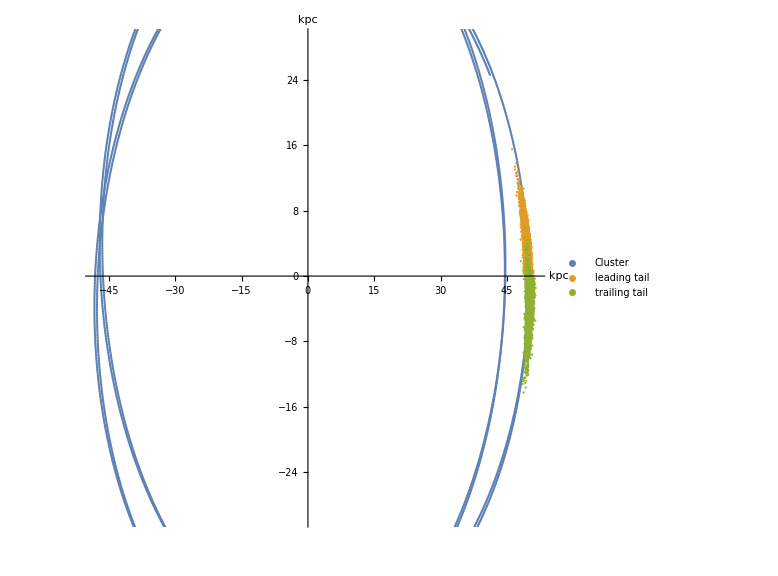

```mathematica
ch23graph = ListPlot[{ch23cl,ch23lt,ch23tt},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"Cluster","leading tail","trailing tail"},AxesLabel->{"kpc","kpc"}]
```

## Differences

c version 8 vs chapel version 21

```mathematica
diffc8ch21cl = Differences[{c8cl,ch21cl}]
diffc8ch21dt = Differences[{c8dt,ch21dt}]
diffc8ch21lt = Differences[{c8lt,ch21lt}]
diffc8ch21ltv = Differences[{c8ltv,ch21ltv}]
diffc8ch21tt = Differences[{c8tt,ch21tt}]
diffc8ch21ttv = Differences[{c8ttv,ch21ttv}]
```

{{0.000036,-1.61672×10^-12}}

{{{2.×10^-7,0.},{-3.×10^-7,0.},{0.,-1.×10^-7},{1.×10^-7,2.×10^-7},{0.,0.},{0.,-5.×10^-7},{0.,0.},{-5.×10^-7,3.×10^-7},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,2.×10^-7},{0.,0.},5971,{0.,-3.×10^-7},{0.,-2.×10^-7},{0.,0.},{0.,0.},{0.,-4.×10^-7},{0.,0.},{-5.×10^-7,3.×10^-7},{-4.×10^-7,0.},{0.,0.},{0.,0.},{0.,2.×10^-7},{0.,0.},{0.,0.},{0.,0.}}}
 |  |  |  |

{{{-0.00001,-0.000031},{0.000011,-0.000019},{0.000011,0.000032},{0.00002,-7.×10^-6},{-0.000011,-0.00003},{0.00003,0.000014},{5.×10^-6,0.000036},5985,{-0.000028,-4.×10^-6},{0.000031,0.},{5.×10^-6,0.},{2.×10^-6,0.},{0.000025,0.},{0.000029,0.},{-0.00003,-2.×10^-8}}}
 |  |  |  |

{{{2.42×10^-10,4.5×10^-10},{-4.87×10^-10,1.2×10^-11},{-2.93×10^-10,-4.77×10^-10},{3.65×10^-10,3.12×10^-10},{1.99×10^-10,-4.05×10^-10},{-2.13×10^-10,3.35×10^-10},5987,{-2.1905×10^-10,-2.86×10^-10},{1.1103×10^-10,-2.79×10^-10},{2.9381×10^-10,-2.71×10^-10},{3.35844×10^-11,-2.64×10^-10},{4.3944×10^-10,-2.66×10^-10},{-3.5978×10^-10,-2.7×10^-10}}}
 |  |  |  |

{{{0.000025,0.000014},{-0.000031,-0.000029},{0.00001,0.000041},{0.000045,-0.000024},{-0.000042,-0.000042},{-0.000018,3.×10^-6},{-0.000024,-6.×10^-6},5985,{-9.×10^-6,4.×10^-6},{0.,0.},{-0.000031,0.},{-0.000035,0.},{0.000024,0.},{-0.000039,0.},{0.000031,1.×10^-7}}}
 |  |  |  |

{{{-1.10701×10^-7,1.55824×10^-7},{-1.11202×10^-7,1.55526×10^-7},{-1.12152×10^-7,1.54955×10^-7},{-1.13014×10^-7,1.54432×10^-7},{-1.13403×10^-7,1.54194×10^-7},{-1.14293×10^-7,1.53644×10^-7},{-1.14746×10^-7,1.53361×10^-7},{-1.15545×10^-7,1.52859×10^-7},{-1.15687×10^-7,1.5277×10^-7},{-1.16463×10^-7,1.52277×10^-7},{-1.17345×10^-7,1.51708×10^-7},5978,{6.9136×10^-9,1.82721×10^-7},{6.41817×10^-9,1.82737×10^-7},{5.32428×10^-9,1.82768×10^-7},{4.69284×10^-9,1.82783×10^-7},{4.13954×10^-9,1.82795×10^-7},{3.37007×10^-9,1.82809×10^-7},{2.24153×10^-9,1.82824×10^-7},{1.78815×10^-9,1.82829×10^-7},{1.05377×10^-9,1.82834×10^-7},{2.71244×10^-10,1.82836×10^-7}}}
 |  |  |  |

c version 8 vs chapel version 22

```mathematica
diffc8ch22cl = Differences[{c8cl,ch22cl}]
diffc8ch22dt = Differences[{c8dt,ch22dt}]
diffc8ch22lt = Differences[{c8lt,ch22lt}]
diffc8ch22ltv = Differences[{c8ltv,ch22ltv}]
diffc8ch22tt = Differences[{c8tt,ch22tt}]
diffc8ch22ttv = Differences[{c8ttv,ch22ttv}]
```

{{0.000036,-1.61672×10^-12}}

{{{0.0240296,-0.069759},{0.11645,-0.006539},{-0.0247932,-0.0158321},{0.093094,0.0365814},{-0.108198,-0.0634503},{0.092161,0.0091291},{0.095952,0.078127},{0.050878,0.133401},{-0.009018,-0.05919},5982,{0.104223,0.033773},{0.034027,0.048976},{0.118867,-0.0550457},{-0.0684875,0.040842},{0.030469,-0.020786},{-0.043363,-0.016455},{-0.05983,-0.0499971},{-0.126056,0.015983}}}
 |  |  |  |

{{{0.01079,0.014769},{0.081111,-0.031719},{-0.012289,-0.008968},{0.01162,-0.075607},{-0.024711,-0.02193},{0.02093,-0.036886},{-0.033095,0.027936},5986,{-0.016769,0.037891},{-0.020995,0.056236},{-0.013898,0.00114},{-0.025475,0.085622},{-0.030471,0.011996},{-0.03133,-0.0163593}}}
 |  |  |  |

{{{1.42×10^-10,3.9×10^-10},{-9.71×10^-10,-2.78×10^-10},{-1.9×10^-10,-4.14×10^-10},{-2.×10^-11,7.7×10^-11},{6.46×10^-10,-1.31×10^-10},{-5.93×10^-10,1.×10^-10},5987,{-7.9524×10^-10,-2.76×10^-10},{4.4304×10^-10,-2.83×10^-10},{1.461×10^-10,-2.7×10^-10},{2.43805×10^-10,-2.66×10^-10},{7.29502×10^-10,-2.67×10^-10},{2.51351×10^-10,-2.7×10^-10}}}
 |  |  |  |

{{{0.056725,0.024114},{0.038069,0.048071},{-0.02129,0.025941},{0.061745,0.046376},{-0.046642,-0.131442},{-0.002018,0.001103},{-0.068024,0.001594},5986,{0.0334,0.045986},{-0.049431,0.081645},{-0.021935,0.05194},{-0.002276,-0.018529},{-0.040139,-0.076934},{0.019531,-0.0035563}}}
 |  |  |  |

{{{-1.10991×10^-7,1.55651×10^-7},{-1.1123×10^-7,1.55509×10^-7},{-1.12218×10^-7,1.54916×10^-7},{-1.12863×10^-7,1.54524×10^-7},{-1.13665×10^-7,1.54032×10^-7},{-1.14255×10^-7,1.53667×10^-7},{-1.14425×10^-7,1.53563×10^-7},{-1.14998×10^-7,1.53205×10^-7},{-1.15929×10^-7,1.52616×10^-7},{-1.16613×10^-7,1.5218×10^-7},{-1.17268×10^-7,1.51758×10^-7},5978,{6.87848×10^-9,1.82722×10^-7},{6.34321×10^-9,1.8274×10^-7},{5.48796×10^-9,1.82764×10^-7},{4.93023×10^-9,1.82778×10^-7},{3.87271×10^-9,1.828×10^-7},{3.56806×10^-9,1.82806×10^-7},{2.14076×10^-9,1.82825×10^-7},{1.70838×10^-9,1.82829×10^-7},{8.11373×10^-10,1.82835×10^-7},{3.48728×10^-10,1.82836×10^-7}}}
 |  |  |  |

chpl version 22 vs c version 9

```mathematica
diffc9ch23cl = Differences[{c9cl,ch23cl}]
diffc9ch23dt = Differences[{c9dt,ch23dt}]
diffc9ch23lt = Differences[{c9lt,ch23lt}]
diffc9ch23ltv = Differences[{c9ltv,ch23ltv}]
diffc9ch23tt = Differences[{c9tt,ch23tt}]
diffc9ch23ttv = Differences[{c9ttv,ch23ttv}]
```

{{{-0.110807,0.155105},{-0.111555,0.154641},{-0.112233,0.154278},{-0.112842,0.15382},{-0.113482,0.15347},{-0.114156,0.153029},{-0.114864,0.152601},5985,{0.00414234,0.182242},{0.00338492,0.182256},{0.00268333,0.182266},{0.0019376,0.182275},{0.00114777,0.182281},{0.00041387,0.182283}}}
 |  |  |  |

{{0.285036,0.460101,-0.0716357,0.0275151,-0.335027,-0.0285637,0.122105,0.0109619,-0.692303,0.0156862,0.0126093,0.25811,0.304917,-0.0373375,0.163119,11971,-0.383077,-0.392168,0.0308878,-0.381426,-0.125798,0.487357,-0.506736,0.318671,-0.446297,-0.248993,-0.570482,-0.216255,-0.110186,0.155469}}
 |  |  |  |

{{{0.023643,-1.35116},{-0.432437,1.81805},{-0.079616,2.05094},{0.085885,-7.1552},{-0.099881,0.479288},{1.05936,-5.01333},{-0.816629,11.7967},{0.624472,-7.90144},5982,{-0.217268,-0.178757},{0.008079,-0.0648277},{-0.017361,0.025264},{0.111007,-0.094543},{-0.089192,0.189338},{-0.285941,0.515138},{-0.274353,-0.246318},{-0.125349,-0.154101}}}
 |  |  |  |

{{{6.37615×10^-9,1.7645×10^-9},{-7.49907×10^-9,-9.03935×10^-10},{-9.211×10^-9,-2.422×10^-9},{2.98559×10^-8,6.61769×10^-10},{-2.03001×10^-9,-2.26716×10^-10},{2.2211×10^-8,1.95498×10^-9},5986,{1.85371×10^-9,-3.85325×10^-11},{-1.5489×10^-10,2.82266×10^-11},{6.09309×10^-10,-2.89345×10^-11},{2.45006×10^-9,-3.52759×10^-11},{2.15936×10^-9,-4.40961×10^-12},{2.76577×10^-9,-3.03532×10^-13}}}
 |  |  |  |

{{{-0.290068,-5.64072},{-0.228084,-1.42814},{-0.087382,-0.9687},{0.458898,2.65863},{0.07402,0.660601},{0.358085,2.8549},{0.261437,3.18925},{0.532587,-5.45215},5983,{0.29924,0.217086},{-0.178079,-0.070398},{-0.27453,0.113601},{-0.292322,0.320472},{0.279841,-0.365617},{-0.175949,-0.10055},{0.141568,0.143598}}}
 |  |  |  |

{{{2.05635×10^-8,2.50702×10^-10},{6.09348×10^-9,-6.49489×10^-10},{3.9761×10^-9,-3.24337×10^-10},{-1.12179×10^-8,1.30478×10^-9},{-2.8728×10^-9,2.31587×10^-10},{-1.24364×10^-8,1.04997×10^-9},5986,{-1.90096×10^-9,3.10666×10^-11},{-1.86528×10^-9,3.09607×10^-11},{2.3547×10^-9,-4.4271×10^-11},{1.55466×10^-9,1.30749×10^-12},{-1.21095×10^-9,2.89951×10^-12},{-1.04844×10^-9,-1.2911×10^-13}}}
 |  |  |  |

## chapel random function

testing random stream’s distribution. Creates an even distribution of numbers between 0 and 1.

Analyzing chapel random stream of 10,000 random numbers

```mathematica
randnum = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ran.csv",{"Data",1;;10000,1}];
randmean = Mean[randnum]
randnumsd = StandardDeviation[randnum]
```

0.500356

0.288492

Analyzing chapel random stream of 10,000 numbers

```mathematica
randnum1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ran1.csv",{"Data",1;;10000,1}];
randmean1 = Mean[randnum]
randnumsd1 = StandardDeviation[randnum]
```

0.500356

0.288492

Analyzing chapel random stream of 5000 numbers

```mathematica
randnum2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ran2.csv",{"Data",1;;5000,1}];
randmean2 = Mean[randnum]
randnumsd2 = StandardDeviation[randnum]
```

0.500356

0.288492

Analyzing chapel random stream of 1000 numbers

```mathematica
randnum3 = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ran3.csv",{"Data",1;;1000,1}];
randmean3 = Mean[randnum]
randnumsd3 = StandardDeviation[randnum]
```

0.500356

0.288492

## C random function

```mathematica
crandnum = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ctest7.csv", {"Data",1,1;;6000}];
crandmean = Mean[crandnum]
crandnumsd = StandardDeviation[crandnum]
```

0.0112011

1.00299

## New Chapel Random function

for 10,000 numbers

```mathematica
nrandnum = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/nran.csv",{"Data",1;;10000,1}];
nrandmean = Mean[nrandnum]
nrandnumsd = StandardDeviation[nrandnum]
```

0.00497026

1.00496

```mathematica
nrandnum1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/nran1.csv",{"Data",1;;10000,1}];
nrandmean1 = Mean[nrandnum1]
nrandnumsd1 = StandardDeviation[nrandnum1]
```

0.00418006

0.995367

```mathematica
nrandnum2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/nran2.csv",{"Data",1;;10000,1}];
nrandmean2 = Mean[nrandnum2]
nrandnumsd2 = StandardDeviation[nrandnum2]
```

-0.0190909

0.992605

## C random function Seeded

ran4

```mathematica
randnum4 = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/ran4.csv",{"Data",1;;5,1}]
randmean4 = Mean[nrandnum3]
randnumsd4 = StandardDeviation[nrandnum3]
```

{520932930,28925691,822784415,890459872,145532761}

0.503698

0.287529

## Chapel random function seeded

nran3

```mathematica
nrandnum3 = Import["/Users/clairerecamier/Desktop/Github/Streakline/P5/RadialOffsets/nran3.csv",{"Data",1;;10000,1}];
nrandmean3 = Mean[nrandnum3]
nrandnumsd3 = StandardDeviation[nrandnum3]
```

0.503698

0.287529